## Formmulae come first

```mathematica
MyGatherBy[items_,crit_]:=Block[{result={},i, found},
Table[
found=False;
For[i=1,i≤ Length[result],i++,
If[crit[item,result[[i,1]]],
result[[i]]=Append[result[[i]],item];
found=True;
i=Length[item]+1
];
];
If[!found,AppendTo[result,{item}]]
,{item, items}
];
result
]
```

```mathematica
MatchPairs[with_,contract_]:=Block[{vertices=Join[with,contract],ws1,cs1,edges={}},
Table[
ws1=SymbolToSets[w1];
Table[
cs1=SymbolToSets[c1];
If[PartitionHasPatternFast[ws1,cs1],
AppendTo[edges,w1->c1]
];
,
{c1,contract}
],
{w1,with}
];
edges
]
```

```mathematica
MpgChainMat2[g_]:=Block[{mpgs,groups, formula},
mpgs=Map[SortEdge,CollectMPGEdges[g]];
groups=MyGatherBy[mpgs,IsomorphicGraphQ[EdgeContract[g,#1],EdgeContract[g,#2]]&];
formula=FindFullFormula4[g];
Table[
Table[
With[{p=MatchPairs[formula, FindFullFormula4[EdgeContract[g,edge[[2]]<->edge[[1]]]]] },
{edge,Length[p]}
]
,{edge,bucket}]
,{bucket,groups}
]
]
```

```mathematica
MpgChainMat2[Graph[plantri[[1]]]]
```

{{{1<->2,0},{1<->3,0},{1<->4,2},{1<->5,2},{1<->6,2},{2<->6,2},{2<->7,2},{2<->8,2},{2<->3,0},{3<->8,2},{3<->9,2},{3<->4,2},{4<->9,2},{4<->10,2},{4<->5,2},{5<->10,2},{5<->11,2},{5<->6,2},{6<->11,2},{6<->7,2},{7<->11,2},{7<->12,2},{7<->8,2},{8<->12,2},{8<->9,2},{9<->12,2},{9<->10,2},{10<->12,2},{10<->11,2},{11<->12,2}}}

```mathematica
GroupBy[{{1<->2,0},{1<->3,0},{1<->4,2},{1<->5,2},{1<->6,2},{2<->6,2},{2<->7,2},{2<->8,2},{2<->3,0},{3<->8,2},{3<->9,2},{3<->4,2},{4<->9,2},{4<->10,2},{4<->5,2},{5<->10,2},{5<->11,2},{5<->6,2},{6<->11,2},{6<->7,2},{7<->11,2},{7<->12,2},{7<->8,2},{8<->12,2},{8<->9,2},{9<->12,2},{9<->10,2},{10<->12,2},{10<->11,2},{11<->12,2}},#[[2]]&]
```

<|0→{{1<->2,0},{1<->3,0},{2<->3,0}},2→{{1<->4,2},{1<->5,2},{1<->6,2},{2<->6,2},{2<->7,2},{2<->8,2},{3<->8,2},{3<->9,2},{3<->4,2},{4<->9,2},{4<->10,2},{4<->5,2},{5<->10,2},{5<->11,2},{5<->6,2},{6<->11,2},{6<->7,2},{7<->11,2},{7<->12,2},{7<->8,2},{8<->12,2},{8<->9,2},{9<->12,2},{9<->10,2},{10<->12,2},{10<->11,2},{11<->12,2}}|>

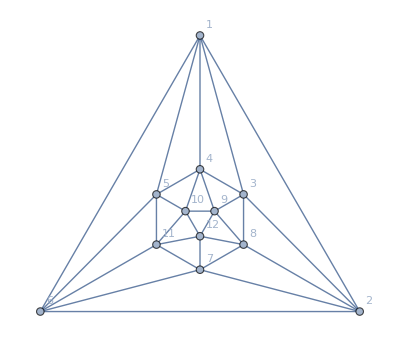

```mathematica
Graph[plantri[[1]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

## Experiments come later

```mathematica
MpgChainMat2[Graph[plantri[[2]]]]
```

{{{},{},{v1ex25adx368bx479c→v1ex25adx368bx79c,v19cx25adx368bx47e→v19cx25adx368bx7e},{v1ex25adx368bx479c→v1ex2adx368bx479c,v1adx25ex368bx479c→v1adx2ex368bx479c},{v1ex25adx368bx479c→v1ex25adx38bx479c,v18bx25adx36ex479c→v18bx25adx3ex479c},{v1ex25adx368bx479c→v1ex25adx368bx49c,v19cx25adx368bx47e→v19cx25adx368bx4e},{v19bdx2acx357ex468→v19bdx2acx357x468,v19bdx246ex358x7ac→v19bdx246x358x7ac},{v18acx2bdx357ex469→v18acx2bdx357x469,v18acx246ex3bdx579→v18acx246x3bdx579},{v19bdx26ax357ex48c→v19bdx26ax357x48c,v19bdx246ex38cx57a→v19bdx246x38cx57a},{v18acx26bx357ex49d→v18acx26bx357x49d,v18acx246ex37bx59d→v18acx246x37bx59d},{v19bdx246ex37cx58a→v19bdx246x37cx58a,v19bdx24cx357ex68a→v19bdx24cx357x68a},{v18acx246ex35dx79b→v18acx246x35dx79b,v18acx24dx357ex69b→v18acx24dx357x69b}},{{v1adx25ex368bx479c→v1adx25ex368bx49c,v19bdx2acx357ex468→v19bdx2acx35ex468,v19bdx24cx357ex68a→v19bdx24cx35ex68a},{},{v19bdx246ex38cx57a→v19bdx26ex38cx57a,v19bdx246ex37cx58a→v19bdx26ex37cx58a,v18bx25adx36ex479c→v18bx25adx36ex79c},{v19cx25adx368bx47e→v19cx2adx368bx47e,v18acx26bx357ex49d→v18acx26bx37ex49d,v18acx24dx357ex69b→v18acx24dx37ex69b},{v1adx25ex368bx479c→v1adx25ex38bx479c,v19bdx246ex37cx58a→v19bdx24ex37cx58a,v19bdx246ex358x7ac→v19bdx24ex358x7ac},{v18acx2bdx357ex469→v18acx2bdx35ex469,v18bx25adx36ex479c→v18bx25adx36ex49c,v18acx24dx357ex69b→v18acx24dx35ex69b},{v19bdx246ex37cx58a→v19bx246ex37cx58a,v19bdx246ex358x7ac→v19bx246ex358x7ac,v18bx25adx36ex479c→v18bx25ax36ex479c},{v19bdx2acx357ex468→v1bdx2acx357ex468,v19bdx26ax357ex48c→v1bdx26ax357ex48c,v18bx25adx36ex479c→v18bx25adx36ex47c},{v19cx25adx368bx47e→v19cx25dx368bx47e,v18acx246ex3bdx579→v18cx246ex3bdx579,v18acx246ex37bx59d→v18cx246ex37bx59d},{v1adx25ex368bx479c→v1adx25ex368x479c,v19bdx26ax357ex48c→v19dx26ax357ex48c,v19bdx24cx357ex68a→v19dx24cx357ex68a},{v18bx25adx36ex479c→v18bx25adx36ex479,v18acx246ex37bx59d→v18ax246ex37bx59d,v18acx246ex35dx79b→v18ax246ex35dx79b},{v19bdx2acx357ex468→v19bx2acx357ex468,v19cx25adx368bx47e→v19cx25ax368bx47e,v19bdx24cx357ex68a→v19bx24cx357ex68a}},{{v19bdx2acx357ex468→v19bdx2acx357ex46,v19bdx26ax357ex48c→v19bdx26ax357ex4c,v19bdx246x357ex8ac→v19bdx246x357exac,v19bdx24cx357ex68a→v19bdx24cx357ex6a,v18acx26bx357ex49d→v1acx26bx357ex49d,v18acx246x357ex9bd→v1acx246x357ex9bd},{v19bdx246x357ex8ac→v1bdx246x357ex8ac,v19bdx24cx357ex68a→v1bdx24cx357ex68a,v18acx2bdx357ex469→v18acx2bdx357ex46,v18acx26bx357ex49d→v18acx26bx357ex4d,v18acx246x357ex9bd→v18acx246x357exbd,v18acx24dx357ex69b→v18acx24dx357ex6b},{v19bdx246ex37cx58a→v1bdx246ex37cx58a,v19bdx246ex357x8ac→v1bdx246ex357x8ac,v18acx246ex3bdx579→v18acx246ex3bdx57,v18acx246ex37bx59d→v18acx246ex37bx5d,v18acx246ex357x9bd→v18acx246ex357xbd,v18acx246ex35dx79b→v18acx246ex35dx7b},{v19bdx246ex38cx57a→v19bdx246ex38cx57,v19bdx246ex37cx58a→v19bdx246ex37cx58,v19bdx246ex357x8ac→v19bdx246ex357x8c,v19bdx246ex358x7ac→v19bdx246ex358x7c,v18acx246ex357x9bd→v18cx246ex357x9bd,v18acx246ex35dx79b→v18cx246ex35dx79b},{v19bdx2acx357ex468→v19bdx2cx357ex468,v19bdx26ax357ex48c→v19bdx26x357ex48c,v19bdx246x357ex8ac→v19bdx246x357ex8c,v19bdx24cx357ex68a→v19bdx24cx357ex68,v18acx246x357ex9bd→v18cx246x357ex9bd,v18acx24dx357ex69b→v18cx24dx357ex69b},{v19bdx2acx357ex468→v19dx2acx357ex468,v19bdx246x357ex8ac→v19dx246x357ex8ac,v18acx2bdx357ex469→v18acx2dx357ex469,v18acx26bx357ex49d→v18acx26x357ex49d,v18acx246x357ex9bd→v18acx246x357ex9d,v18acx24dx357ex69b→v18acx24dx357ex69},{v19bdx246ex357x8ac→v19dx246ex357x8ac,v19bdx246ex358x7ac→v19dx246ex358x7ac,v18acx246ex3bdx579→v18acx246ex3dx579,v18acx246ex37bx59d→v18acx246ex37x59d,v18acx246ex357x9bd→v18acx246ex357x9d,v18acx246ex35dx79b→v18acx246ex35dx79},{v19bdx246ex38cx57a→v19bdx246ex38x57a,v19bdx246ex37cx58a→v19bdx246ex37x58a,v19bdx246ex357x8ac→v19bdx246ex357x8a,v19bdx246ex358x7ac→v19bdx246ex358x7a,v18acx246ex3bdx579→v18ax246ex3bdx579,v18acx246ex357x9bd→v18ax246ex357x9bd},{v19bdx2acx357ex468→v19bdx2ax357ex468,v19bdx26ax357ex48c→v19bdx26ax357ex48,v19bdx246x357ex8ac→v19bdx246x357ex8a,v19bdx24cx357ex68a→v19bdx24x357ex68a,v18acx2bdx357ex469→v18ax2bdx357ex469,v18acx246x357ex9bd→v18ax246x357ex9bd},{v19bdx26ax357ex48c→v19bx26ax357ex48c,v19bdx246x357ex8ac→v19bx246x357ex8ac,v18acx2bdx357ex469→v18acx2bx357ex469,v18acx26bx357ex49d→v18acx26bx357ex49,v18acx246x357ex9bd→v18acx246x357ex9b,v18acx24dx357ex69b→v18acx24x357ex69b},{v19bdx246ex38cx57a→v19bx246ex38cx57a,v19bdx246ex357x8ac→v19bx246ex357x8ac,v18acx246ex3bdx579→v18acx246ex3bx579,v18acx246ex37bx59d→v18acx246ex37bx59,v18acx246ex357x9bd→v18acx246ex357x9b,v18acx246ex35dx79b→v18acx246ex35x79b},{v19bdx246ex38cx57a→v19bdx246ex3cx57a,v19bdx246ex37cx58a→v19bdx246ex37cx5a,v19bdx246ex357x8ac→v19bdx246ex357xac,v19bdx246ex358x7ac→v19bdx246ex35x7ac,v18acx246ex37bx59d→v1acx246ex37bx59d,v18acx246ex357x9bd→v1acx246ex357x9bd}}}

```mathematica
Table[MpgChainMat2[ReadGrof[k]],{k,1,3}]
```

{{{{1<->2,0},{1<->3,0},{1<->4,0},{2<->3,0},{2<->4,0},{3<->4,0}}},{{{1<->2,0},{1<->3,0},{1<->5,0},{2<->4,1},{3<->4,1},{4<->5,0}}},{{{1<->2,0},{1<->3,0},{1<->5,0},{2<->6,0},{3<->4,1},{4<->5,0},{4<->6,0}}}}

```mathematica
Select[Range[50000],With[{g=ReadGrof[#]},If[Min[VertexDegree[g]]<5,False,True]]&]
```

{6985}

```mathematica
Monitor[Select[Range[50000,100000],With[{g=ReadGrof[#]},k=#;If[Min[VertexDegree[g]]<5,False,True]]&],k]
```

{}

```mathematica
VertexDegree[GraphData["DodecahedralGraph"]]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
VertexDegree[GraphData["IcosahedralGraph"]]
```

{5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
IsomorphicGraphQ[GraphData["IcosahedralGraph"],ReadGrof[6985]]
```

True

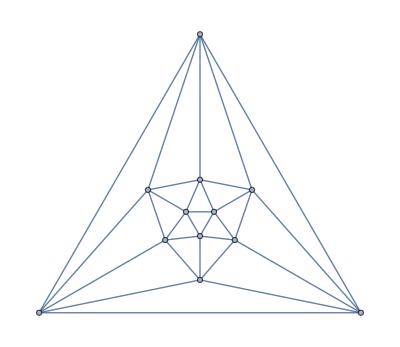

```mathematica
GraphData["IcosahedralGraph"]
```

```mathematica
VertexDegree[ReadGrof[6985]]
```

{5,5,5,5,5,5,5,5,5,5,5,5}